```mathematica
zeta=0.2;epsilon=0.03;delta=0.1;
```

```mathematica
f[p_]:=If[p>=1-zeta,1-zeta,1-zeta-(1-zeta-p)(1-epsilon)]
```

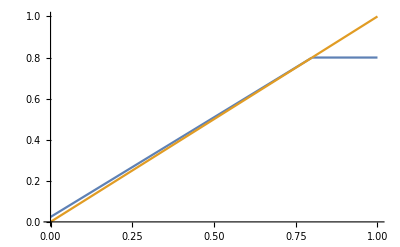

```mathematica
Plot[{f[p],p},{p,0,1},PlotRange->{{0,1},{0,1}}]
```